```mathematica
(*Dillon Skeehan. Physics 732 Final*)
ClearAll[h0,h1,Δ1, Δ2, Δ3, Δ4,ΔL, ΔR,ϵin,v,u,u1,rotTwoπ, rotOneπ,rotHalfπ]
(*Define constants*)
ℏ = 6.58*10^-16;
Δ1 = 2.62;
Δ2 = 3.5;
Δ3 = 4.6;
Δ4 = 1.65;
ΔL = 52.7;
ΔR = 9.2;
ϵin = -1000;
v=100;
(*Set up Hamiltonian Matrix from Nat. Commun Paper *)
ham[ϵ_,t_] = ({{ϵ/2+v*t/2, 0, Δ1, -Δ2}, {0, ϵ/2+v*t/2+ΔL, -Δ3, Δ4}, {Δ1, -Δ3, -ϵ/2-v*t/2, 0}, {-Δ2, Δ4, 0, -ϵ/2-v*t/2+ΔR}});
```

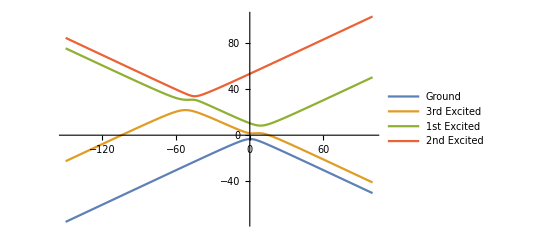

```mathematica
(*The Eigenvalues of this hamiltonian are hard to work with algebraically so its better just to have a graphical representation *)
Plot[Evaluate[Eigenvalues[ham[ϵ,0]]], {ϵ, -150,100},PlotLegends-> {"Ground", "3rd Excited", "1st Excited", "2nd Excited"}]
```

```mathematica
(*Next we will find the minimal energy gaps. Since the algebraic expressions for the eigenvalues are hard to work with we will have to use a table of the values. We can evaluate at many points and see where the minimum distance is. *)
(*This first gap corresponds to roughly twice Δ4 *)Min[Table[(Eigenvalues[ham[-1000,t]][[1]]-Eigenvalues[ham[-1000,t]][[2]]),{t,9,10.5,.001}]]
```

3.09254

```mathematica
(*This second gap corresponds to roughtly twice Δ3 *)
```

```mathematica
Min[Table[(Eigenvalues[ham[-1000,t]][[2]]-Eigenvalues[ham[-1000,t]][[4]]),{t,9,9.75,.001}]]
```

8.9235

```mathematica
(*This third gap corresponds to roughly twice Δ2 *)
```

```mathematica
Min[Table[(Eigenvalues[ham[-1000,t]][[2]]-Eigenvalues[ham[-1000,t]][[4]]),{t,9.75,10.5,.001}]]
```

6.62262

```mathematica
(*This final gap correspond roughly to twice Δ1*)
```

```mathematica
Min[Table[(Eigenvalues[ham[-1000,t]][[4]]-Eigenvalues[ham[-1000,t]][[3]]),{t,9,10.5,.001}]]
```

4.98081

```mathematica
(*The location of the minimum energy difference between the ground and first excited state occurs at t->10.0049 making for an bias value of about ϵ = .49 *)
```

```mathematica
Solve[(Eigenvalues[ham[-1000,t]][[4]]-Eigenvalues[ham[-1000,t]][[3]]) == 4.98,t]
```

{{t→9.46106},{t→9.47714},{t→9.48088},{t→9.56872},{t→9.96652},{t→10.0049},{t→10.0835},{t→10.0954}}

```mathematica
(*Lets develop the time evolution operator for our hamiltonian. This this is a time dependent hamiltonian, we approximate the integral in the exponent by a large product of different matrix exponents. *)
```

```mathematica
ClearAll@constructU;
constructU::usage="constructU[h,tinit,tfinal,n]";constructU[h_, tinit_,tfinal_,n_] := Module[{dt = N[(tfinal - tinit)/n], curVal = IdentityMatrix[Length@h[0]]}, Do[curVal = MatrixExp[-I*h[t]*dt].curVal, {t, tinit, tfinal-dt, dt}]; curVal]
(*Using the very helpful advice found at http://mathematica.stackexchange.com/questions/21751/solving-a-time-dependent-schroedinger-equation/21781#21781 *)
```

```mathematica
(*now we can create the time evolution operator with initial time 0 and good accuracy*)
```

```mathematica
u[ϵ_,τ_] := constructU[ham[ϵ,#]&,0,τ,500];
```

```mathematica
(*Lets plot the probability of being in any of the states with respect to time*)
```

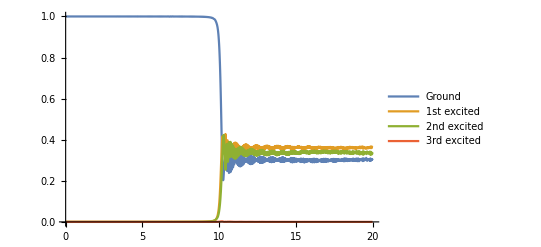

```mathematica
Plot[{Abs[{1,0,0,0}.u[ϵin, τ].{1,0,0,0}]^2,Abs[{0,0,1,0}.u[ϵin,τ].{1,0,0,0}]^2,Abs[{0,0,0,1}.u[ϵin,τ].{1,0,0,0}]^2,Abs[{0,1,0,0}.u[ϵin,τ].{1,0,0,0}]^2}  ,{τ,0,20},PlotLegends->{"Ground", "1st excited", "2nd excited", "3rd excited"}]
```

```mathematica
(*We see the transition probablities level off after the avoided crossings are dealt with*)
(*The probability that we are still in the ground state*)
Abs[{1,0,0,0}.u[ϵin,20].{1,0,0,0}]^2
```

0.300377

```mathematica
(*The probability that we are in the first excited state*)
Abs[{0,1,0,0}.u[ϵin,20].{1,0,0,0}]^2
```

0.0000118524

```mathematica
(*The probability that we are in the 2nd excited state *)
Abs[{0,0,1,0}.u[ϵin,20].{1,0,0,0}]^2
```

0.361284

```mathematica
(*The probability that we are in the 3rd excited state *)
Abs[{0,0,0,1}.u[ϵin,20].{1,0,0,0}]^2
```

0.338327

```mathematica
(*The Landau Zener formula gives a reasonable approximation to the ground state probability*)
lz = Exp[-2*π*(Δ2+1)^2/100]
```

0.280174

```mathematica
(*We can now try to calculate X rotations*)
```

```mathematica
(*For an X-Rotation we start in ground state at large negative ϵ and then are quickly brought to the configuration with the minimal level separation between the ground and first excited state. This occurs at ϵ = .49. The system stays in this configuration for tx time. The hamiltonian in this case is constant in time so we can define the time evolution operator as a simple matrix exponential *)
```

```mathematica
u1[ϵ_,t_] = MatrixExp[-I * ham[ϵ,0]*t];
```

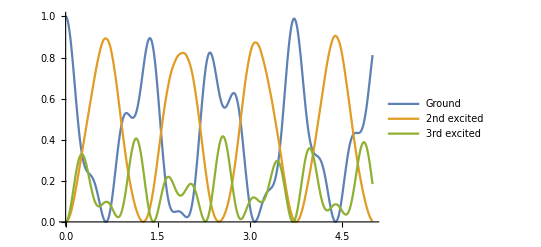

```mathematica
Plot[{Abs[{1,0,0,0}.u1[.49,t].{1,0,0,0}]^2,Abs[{0,0,1,0}.u1[.49,t].{1,0,0,0}]^2,Abs[{0,0,0,1}.u1[.49,t].{1,0,0,0}]^2},{t,0,5},PlotLegends->{"Ground", "2nd excited", "3rd excited"}]
```

```mathematica
(*A pi rotation should transform the ground state into a super position of the 2nd and 3rd excited states,while a 2pi rotation should put us back in the original ground state. From the the graph we see that *)
rotTwoπ = 3.7;
rotOneπ = 1.85;
rotHalfπ = .8;
```

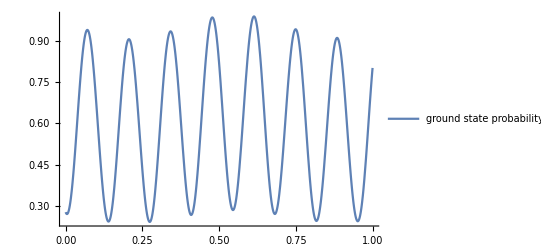

```mathematica
(*In order to model the ramsey experiment we start with an initial energy ϵ = -40. We then pulse to the minimal energy step between the ground stated and the first excited state. We perform a X(pi/2) rotation and then pulse to ϵ = 45. We wait in this state for time tp and and then pulse back to the minimal energy step state and perform another X(pi/2) rotation. Finally we return to our original energy and perform a measurement.*)
Plot[Abs[{1,0,0,0}.u1[.49,.8].u1[45.49,tp].u1[.49,.8].{1,0,0,0}]^2,{tp,0,1}, PlotLegends->{"ground state probability"}]
```

```mathematica
(*We are approximating the pulses as instantaneous perturbations that do not change the given state we are in. Also note that this produces sinuosoidal behavior which is what we would expect having undergone 2 pi/2 rotations.*)
```